```mathematica
n={3,4,5,6};
a=1/2^2-1/n^2;
lamCCD1={656.29,486.18,434.07,410.19}*10^(-7);
nuCCD1=1/lamCCD1;
dataCCD1=Transpose[{a,nuCCD1}];
NonlinearModelFit[dataCCD1,k*x,{k},x]
```

FittedModel[109704. x]

```mathematica
%18["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 109704. | 1.69425 | 64750.5 | 8.12346×10^-15

```mathematica
lamCCD2={656.12,486.06,433.94,410.13}*10^(-7);
nuCCD2=1/lamCCD2;
dataCCD2=Transpose[{a,nuCCD2}];
NonlinearModelFit[dataCCD2,k*x,{k},x]
```

FittedModel[109729. x]

```mathematica
%23["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 109729. | 3.88277 | 28260.4 | 9.77089×10^-14

```mathematica
lamPMT1={656.47,486.08,434.15,410.29}*10^(-7);
nuPMT1=1/lamPMT1;
dataPMT1=Transpose[{a,nuPMT1}];
NonlinearModelFit[dataPMT1,k*x,{k},x]
```

FittedModel[109690. x]

```mathematica
%28["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 109690. | 10.1694 | 10786.3 | 1.75733×10^-12

```mathematica
lamPMT2={656.28,485.94,434.02,410.18}*10^(-7);
nuPMT2=1/lamPMT2;
dataPMT2=Transpose[{a,nuPMT2}];
NonlinearModelFit[dataPMT2,k*x,{k},x]
```

FittedModel[109721. x]

```mathematica
%33["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 109721. | 10.3876 | 10562.7 | 1.87132×10^-12

```mathematica
lamStandardH={656.473,486.276,434.175,410.296}*10^(-7);
nuStandardH=1/lamStandardH;
dataStandardH=Transpose[{a,nuStandardH}];
NonlinearModelFit[dataStandardH,k*x,{k},x]
```

FittedModel[109677. x]

```mathematica
%50["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 109677. | 0.0437482 | 2.50701×10^6 | 1.3996×10^-19

```mathematica
lamStandardD={656.294,486.143,434.057,410.183}*10^(-7);
nuStandardD=1/lamStandardD;
dataStandardD=Transpose[{a,nuStandardD}];
NonlinearModelFit[dataStandardD,k*x,{k},x]
```

FittedModel[109707. x]

```mathematica
%55["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 109707. | 0.0593884 | 1.84728×10^6 | 3.49842×10^-19

```mathematica
RInf=109737.31;
mp=1.672621637*10^(-27);
me=9.1093826*10^(-31);
RH=RInf*mp/(mp+me);
RD=RInf*(2*mp)/(2*mp+me);
NumberForm[RH,16]
NumberForm[RD,16]
```

109677.5777212823

109707.4357300509

```mathematica
me/mp
```

0.000544617

```mathematica
NumberForm[0.0005446276550827616,16]
```

0.0005446276550827616

```mathematica
MassRatio[lamD_,lamSpace_]:=Module[{data},data=Transpose[{lamD/2,lamSpace}];NonlinearModelFit[data,k*x,{k},x]]
```

```mathematica
MassRatio[{656.294,486.143,434.057,410.183},{0.179,0.133,0.118,0.113}]
```

FittedModel[0.000546448 x]

```mathematica
FittedModel[Panel[Short[0.0005464484927800202 x,2],FrameMargins->5]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 0.000546448 | 1.32353×10^-6 | 412.872 | 3.13339×10^-8

```mathematica
MassRatio[{656.12,486.06,433.94,410.13},{0.17,0.12,0.13,0.06}]
```

FittedModel[0.00049037 x]

```mathematica
FittedModel[Panel[Short[0.0004903700179399032 x,2],FrameMargins->5]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 0.00049037 | 0.0000545791 | 8.98457 | 0.00291032

```mathematica
MassRatio[{656.28,485.94,434.02,410.18},{0.17,0.12,0.13,0.06}]
```

FittedModel[0.000490324 x]

```mathematica
FittedModel[Panel[Short[0.0004903235720631093 x,2],FrameMargins->5]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 0.000490324 | 0.0000545665 | 8.98579 | 0.00290918

```mathematica
Ratio[Dl_,l_]:=2*Dl/l;
DR[Dl_,l_,dDl_,dl_]:=Module[{aa,cc,x,y},aa={x->Dl,y->l};
SqrtSum[a_,b_]:=Sqrt[a^2+b^2];
cc=SqrtSum[dDl*D[Ratio[x,y],x]/.aa,dl*D[Ratio[x,y],y]/.aa];cc]
```

```mathematica
DR[0.17,656.28,0.05,0.1]
```

0.000152374

```mathematica
Ratio[0.17,656.28]
```

0.000518072

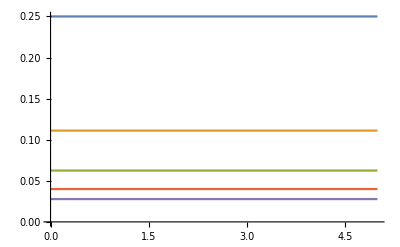

```mathematica
Plot[{1/4,1/9,1/16,1/25,1/36},{x,0,5}]
```

```mathematica
Plot[{1/4,1/9,1/16,1/25,1/36},{x,0,5},PlotTheme->Automatic]
```

-Graphics-